```mathematica
Clear["Global`*"]
```

```mathematica
(* g is an increasing function of z. *)
cond1=g*(2-Qdg)-1;
eq1=Collect[Simplify[(1-z)*gy+z*gz-g/.{gy->Qdg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gy^2+(g-(1-z)*gy)^2-z*g2/.{gy->Qdg*g+1-g}],g2];
M1=-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z;
M2=2 (1+g (-2+Qdg))(-2+Qdg) ;
M3=(-2+Qdg);
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=FullSimplify[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}]
```

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

{(1+g (-3+Qdg)) (1+g (-1+Qdg)) (-Qcg+Qdg),(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z}

```mathematica
FullSimplify[Expand[(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)+(M1+M2)*(Qcg-Qdg)]]
```

-(Qcg-Qdg) ((-3+2 Qdg) (-1+z)+2 g (-2+(-3+Qdg) Qdg (-1+z)+z)+g^2 (-4+(-4+Qdg) Qdg (-1+z)+3 z))

```mathematica
inh=Expand[(g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z]
inM1M2=FullSimplify[Expand[M1+M2]]
```

1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z

2 g (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 (-2+Qdg) (-1+z)

```mathematica
inh+inM1M2
```

-3+4 g+4 g^2+2 Qdg-6 g Qdg-4 g^2 Qdg+2 g Qdg^2+g^2 Qdg^2+3 z-2 g z-3 g^2 z-2 Qdg z+6 g Qdg z+4 g^2 Qdg z-2 g Qdg^2 z-g^2 Qdg^2 z

```mathematica
Collect[Expand[h],Qdg]
```

1-2 g+Qcg-4 g Qcg+4 g^2 Qcg-Qcg z+4 g Qcg z-3 g^2 Qcg z+Qdg^3 (-g^2+g^2 z)+Qdg^2 (-2 g+4 g^2+g^2 Qcg+2 g z-4 g^2 z-g^2 Qcg z)+Qdg (-1+5 g-4 g^2+2 g Qcg-4 g^2 Qcg+z-4 g z+3 g^2 z-2 g Qcg z+4 g^2 Qcg z)

```mathematica
FullSimplify[1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z-k1]
```

3+4 Qcg-5 Qdg+g^2 (4-(-4+Qdg) Qdg (-1+z)-3 z)+2 (Qcg-Qdg) (Qdg (-1+z)-2 z)-z+2 g ((-Qcg (-2+Qdg)+(-1+Qdg)^2) (-2+Qdg)+(2+Qcg (-3+Qdg) (-1+Qdg)-(-2+Qdg)^2 Qdg) z)

```mathematica
Collect[k1-h,Qcg]
```

-3-g (-2+Qdg)+Qdg-2 (-2+Qdg) (Qdg+g (-2+Qdg) Qdg)+2 Qdg (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z+Qdg ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)+Qcg (2 (1+g (-2+Qdg)) (-2+Qdg)-(g+(1+g (-1+Qdg)) (-1+z))^2-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z+(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z
```

1-4 g+4 g^2+2 (1+g (-2+Qdg)) (-2+Qdg)+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z

```mathematica
Expand[M1+M2]
```

1/2 (-4+8 g+2 Qdg-8 g Qdg+2 g Qdg^2+4 z-6 g z-2 Qdg z+8 g Qdg z-2 g Qdg^2 z)

```mathematica
Expand[4-(-4+Qdg) Qdg (-1+z)-3 z]
```

4-4 Qdg+Qdg^2-3 z+4 Qdg z-Qdg^2 z

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[out<  0]]
```

g<√((-1+Qdg+Qcg (-1+z)-Qdg z)/((Qcg-Qdg) (-4+(-4+Qdg) Qdg (-1+z)+3 z)))

```mathematica
FullSimplify[(M1+M2)*(Qcg-Qdg)-h]
```

-1-g (-2+Qdg)+(Qcg-Qdg) (2 g (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 (-2+Qdg) (-1+z))-(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
FullSimplify[(M1+M2)*(Qcg-Qdg)+h]
```

1+g (-2+Qdg)+(Qcg-Qdg) (2 g (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 (-2+Qdg) (-1+z))+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
Simplify[(M1+M2)*(Qcg-Qdg)+M3-k1]
```

0

```mathematica
MH = -1-(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z);
```

```mathematica
out=FullSimplify[Expand[(M1+M2)*(Qcg-Qdg)*g+MH]]
```

-1+Qdg-Qdg z+Qcg (-1+g^2 (4-(-4+Qdg) Qdg (-1+z)-3 z)+z)+g^2 Qdg (-4+(-4+Qdg) Qdg (-1+z)+3 z)

```mathematica
(4-(-4+Qdg) Qdg (-1+z)-3 z)
```

```mathematica
ou1=FullSimplify[-1+Qdg-Qdg z-Qcg +Qcg *z]
out2a=FullSimplify[(4-(-4+Qdg) Qdg (-1+z)-3 z)]
out2=(Qcg-Qdg)*g^2*out2a;
```

-1+Qdg+Qcg (-1+z)-Qdg z

4-(-4+Qdg) Qdg (-1+z)-3 z

```mathematica
outa=FullSimplify[Expand[out2a*g^2-1+z]]
```

-1+g^2 (4-(-4+Qdg) Qdg (-1+z)-3 z)+z

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[outa*(Qcg-Qdg)≤  1]]
```

g≤√((-1+Qdg+Qcg (-1+z)-Qdg z)/((Qcg-Qdg) (-4+(-4+Qdg) Qdg (-1+z)+3 z)))

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[(M1+M2)*(Qcg-Qdg)<  -M3]]
```

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

```mathematica
Together[Qcg*g+1-g]
```

(-e+e^2+2 e g-3 e^2 g-2 e g^2+3 e^2 g^2+e g^3-e^2 g^3-g ϵ+2 e g ϵ+g^2 ϵ-2 e g^2 ϵ-g^3 ϵ+g^3 ϵ^2)/((-e+e g-g ϵ) (1-e+e g-g ϵ))

```mathematica
numdomzx=NumeratorDenominator[Together[Qcg*g+1-g]];
polyzx = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzx[[2]]]]*numdomzx[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
```

```mathematica
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a1>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a2>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a3>0]]
```

True

2 (1+e) ϵ>e+3 ϵ^2

2 (1+e) ϵ>e+3 ϵ^2

True

```mathematica
polyzx
```

e-e^2-2 e g+3 e^2 g+2 e g^2-3 e^2 g^2-e g^3+e^2 g^3+g ϵ-2 e g ϵ-g^2 ϵ+2 e g^2 ϵ+g^3 ϵ-g^3 ϵ^2

```mathematica
numdomgx=NumeratorDenominator[Together[Qcg*g+1-g]];
numdomgy=NumeratorDenominator[Together[Qdg*g+1-g]];
numdomgz=NumeratorDenominator[Together[Qdg*g+1-g]];
polygx = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgx[[2]]]]*numdomgx[[1]];
polygy = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgy[[2]]]]*numdomgy[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
polygz = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgz[[2]]]]*numdomgz[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
```

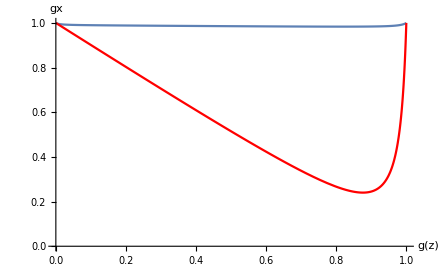

```mathematica
Show[{Plot[Evaluate[Qcg*g+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","gx"},PlotRange->{0,1}],
Plot[Evaluate[Qdg*g+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","gy"},PlotStyle->Red,PlotRange->{0,1}]}]
```

```mathematica
Collect[g-z*(g2*(Qcg-Qdg)+Qdg*g+1-g)-(1-z)*(Qcg*g+1-g),z]
```

-1+2 g-g Qcg+(g Qcg-g2 (Qcg-Qdg)-g Qdg) z

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

```mathematica
FullSimplify[D[Qdg,g]]
```

((-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3)/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>0,FullSimplify@Reduce[D[Qcg*g,g]>1]]
```

$Aborted

```mathematica
sol=(-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3-(-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2
```

```mathematica
FullSimplify[(-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3-(-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2]
```

-g (e-ϵ)^2 (e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ)))

```mathematica
e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ))
```

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>0,FullSimplify@Reduce[e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ))<0]]
```

$Aborted

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

```mathematica
Plot[Evaluate[G//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πy"}]}
```

```mathematica
mysol=Solve[r*(Qcg-Qdg)*z==1/.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01,g->x*},x];
```

{{g→0},{g→1}}

```mathematica
Solve[gx==Qcg&&gy==Gdg&&gz==gx*g+gy*(1-g)&&g==(1-y-z)*gx+y*gy+z*gz]
```

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>0&&g==(1-y-z)*gx+y*gy+z*gz&&gx==Qcg&&gy==Gdg&&gz==gx*g+gy*(1-g),FullSimplify@Solve[r*z*(gx-gy)==1]]
```

{{gy→gx-1/(r z)}}

```mathematica
solyplot=Solve[gx==Qcg&&gz==Qcg*g+(Qcg-1/r*z)*(1-g)/.{g->gx*(1-y-z)+gz*z+y*(gx-1/r*z)},{gx,gz}]//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01};
```

```mathematica
Plot[Evaluate[gx/.solyplot],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πy"}]
```

```mathematica
g=gx*(1-y-z)+gz*z+y*gy
```

gy y+gx (1-y-z)+gz z

```mathematica
sol1=Solve[gx==Qcg&&gy==Qdg&&gz==Qcg*g+Qdg*(1-g),{gx,gy,gz}]//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01};
```

```mathematica
Solve[r*(gx-gy)*z==1,gx]
```

{{gx→(1+gy r z)/(r z)}}

```mathematica
Solve[gz-gy==((1-y-z)*gx+y*gy+z*gz)*(gx-gy),{z}]
```

{{z→(gx^2+gy-gx gy-gz-gx^2 y+2 gx gy y-gy^2 y)/((gx-gy) (gx-gz))}}

```mathematica
Simplify[(1-gx)*(Qcg*g+Qcb*(1-g))-gx*((1-Qcg)*g+(1-Qcb)*(1-g))]
```

-gx+Qcb-g Qcb+g Qcg

```mathematica
Simplify[(gy-gy2)*(Qdg*g+Qdb*(1-g))-gy2*((1-Qdg)*g+(1-Qdb)*(1-g))]
```

-gy2+gy (Qdb-g Qdb+g Qdg)

```mathematica
Collect[(1-gz)*(Qcg*g2+(Qdg+Qcb)*(g-g2)+(1-2*g+g2)*Qdb)-gz*((1-Qcg)*g2+(2-Qdg-Qcb)*(g-g2)+(1-2*g+g2)*(1-Qdb)),g2]
```

-gz+2 g gz (1-Qdb)+(1-gz) Qdb-2 g (1-gz) Qdb+gz Qdb-g gz (2-Qcb-Qdg)+g (1-gz) (Qcb+Qdg)+g2 (-gz (1-Qcg)+(1-gz) Qcg-gz (1-Qdb)+(1-gz) Qdb+gz (2-Qcb-Qdg)+(-1+gz) (Qcb+Qdg))

```mathematica
Simplify[1-g-1+2*g-g2]
```

g-g2

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
```

```mathematica
FullSimplify[Qcb-Qdb]
```

-((-1+g) g (e-ϵ)^2)/((-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ))

```mathematica
FullSimplify[Qcg-Qdg]
```

((-1+g) g (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Collect[g-gx*x-gy*y-gz*z/.{gx->Qcg*g+Qcb*(1-g),gy->Qdg*g+Qdb*(1-g),gz->Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2)},g2]
```

g-((1-g) Qcb+g Qcg) x-((1-g) Qdb+g Qdg) y-Qdb z+2 g Qdb z-g (Qcb+Qdg) z+g2 (-Qcg z-Qdb z+(Qcb+Qdg) z)

```mathematica
eqn1=FullSimplify[ g-((1-g) Qcb+g Qcg) x-((1-g) Qdb+g Qdg) y-Qdb z+2 g Qdb z-g (Qcb+Qdg) z];
```

```mathematica
eqn2a=Simplify[x*z*gx^2+y*z*gy^2+(g-x*gx-y*gy)^2/.{gx->Qcg*g+Qcb*(1-g),gy->Qdg*g+Qdb*(1-g)}];
```

```mathematica
eqn2=FullSimplify[(Qcg-Qcb-Qdg+Qdb)*eqn2a];
```

```mathematica
Solve[eqn1==eqn2,g];
```

```mathematica
Solve[gx==Qcg*g+Qcb*(1-g),g];
```

```mathematica
Solve[(1-gz)*(Qcg*g2+Qdg*(g-g2))==gz*((1-Qcg)*g2+(1-Qdg)*(g-g2)+1-g),gz]
```

{{gz→g2 Qcg+g Qdg-g2 Qdg}}

```mathematica
Solve[g==Qcg*g^2+Qdg*(g-g^2),g]
```

{{g→0},{g→1}}

```mathematica
Simplify[(1-gx)*Qcg*-gx*(1-Qcg)*g]
```

-g (-1+gx) gx (-1+Qcg) Qcg

```mathematica
Simplify[(1-gz)*(Qcg*g2+(g-g2)*Qdg)-gz*((1-Qcg)*g2+(g-g2)*(1-Qdg))]
```

g2 (Qcg-Qdg)+g (-gz+Qdg)

```mathematica
D[Qdg*g,g]/.{g->1}
```

2-((1-e) (e-ϵ))/(1-ϵ)-(e (-e+ϵ))/ϵ

```mathematica
Simplify[-((e-ϵ) ϵ)/e-((1-ϵ) (-e+ϵ))/(1-e)]
```

-(e-ϵ)^2/((-1+e) e)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qcg,g]>1/.{g->0}]]
```

True

```mathematica
D[Qcg*g^2+Qdg*(g-g^2),g]/.{g->1}
```

2

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qcg*g+1-g,{g,2}]>1/.{g->0}]]
```

True

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[1>D[Qcg*g+Qcb*(1-g),g]>-1/.{g->1/2}].Reals]
```

((e>Root[4 ϵ^2-5 ϵ^3+2 ϵ^4+(8 ϵ-9 ϵ^2+2 ϵ^3) #1+(4-15 ϵ+6 ϵ^2) #1^2+(-3+6 ϵ) #1^3&,1]&&e+ϵ<1)||e>Root[4 ϵ^2-5 ϵ^3+2 ϵ^4+(8 ϵ-9 ϵ^2+2 ϵ^3) #1+(4-15 ϵ+6 ϵ^2) #1^2+(-3+6 ϵ) #1^3&,3]).ℝ

```mathematica
Simplify[D[Qcg*g+Qcb*(1-g),g]/.{g->1/2}]
```

(-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2))/((-2+e+ϵ)^2 (e+ϵ)^2)

```mathematica
-3 e^4+12 e^3 ϵ-4 e ϵ (-2+ϵ^2)+ϵ^2 (4-8 ϵ+5 ϵ^2)+e^2 (4-24 ϵ+6 ϵ^2)
```

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2)<(-2+e+ϵ)^2 (e+ϵ)^2]]
```

e+ϵ<1

```mathematica
FullSimplify[-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2)]
```

-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2+3 (-3+ϵ) ϵ)+ϵ^2 (4+3 (-2+ϵ) ϵ)

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qdg*g+Qdb*(1-g),g]<1/.{g->1/2}]]
```

True

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qcg*g^2+(Qcb-Qdb)*(g-g^2)+Qdb*(1-2*g+g^2),g]<1/.{g->1/2}]]
```

True

```mathematica
D[Qcg*g+Qcb*(1-g),g]/.{g->1/2,e->0.1,ϵ->0.9}
```

1.

```mathematica
Solve[g==Qcg*g+Qcb*(1-g),g]
```

{{g→0},{g→0},{g→1/2},{g→1},{g→1}}

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qcg*g+Qcb*(1-g),g]<1/.{g->1}]]
```

False

```mathematica
D[Qcg*g+Qcb*(1-g),g]/.{g->0}
```

1

```mathematica
Collect[-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2),e]
```

-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2)

```mathematica
Solve[2-9 ϵ+3 ϵ^2==0,ϵ]
```

{{ϵ→1/6 (9-√57)},{ϵ→1/6 (9+√57)}}

```mathematica
Solve[4-6ϵ+3 ϵ^2==0,ϵ]
```

{{ϵ→1/3 (3-ⅈ √3)},{ϵ→1/3 (3+ⅈ √3)}}

```mathematica
Simplify[(1-g)*(Qcg*g+Qcb*(1-g))-g*((1-Qcg)*g+(1-Qcb)*(1-g))]
```

Qcb+g (-1-Qcb+Qcg)

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[D[Qcg*g+Qcb*(1-g),g]<1/.{g->1/2}]]
```

e+ϵ<1

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg*g^2+Qdg*(g-g^2)+1-2*g>0]]
```

True

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qdg*g+1-2*g>0]]
```

(3 e==1&&3+3 ϵ (-1+g (-2+6 ϵ))<√(9-42 ϵ+81 ϵ^2))||(e^2 (-3+6 g)+ϵ (-1+2 g (1+ϵ))+2 e (1+ϵ-g (1+4 ϵ))<√(-3 e^4-6 e^2 ϵ+ϵ^2+4 e^3 (1+ϵ))&&3 e≠1)

```mathematica
Simplify[(1-g)*(Qcg*g+Qcb*(1-g))-g*((1-Qcg)*g+(1-Qcb)*(1-g))]
```

Qcb+g (-1-Qcb+Qcg)

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg+1-2*g≥0]]
```

True

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg*g^2+Qdg*(1-g)*g+1-2*g≥0]]
```

True

```mathematica
Solve[e==Qdg,g]/.{ϵ->0.9802,e->0.01}
```

{{g→-0.083433},{g→0.0627129}}

```mathematica
Solve[ϵ==Qcg,g]/.{ϵ->0.9802,e->0.01}
```

{{g→1.26428},{g→0.840731}}

```mathematica
ϵ*g+e*(1-g)/.{ϵ->0.9802,e->0.01,g->0.06271294100697586}
```

0.0708441

```mathematica
ϵ*g+e*(1-g)/.{ϵ->0.9802,e->0.01,g->0.8407313826830128}
```

0.825678

```mathematica
Solve[(1-gz)*(Qcg*g+Qdg*(1-g))==gz*((1-Qcg)*g+(1-Qdg)*(1-g)),gz]
```

{{gz→g Qcg+Qdg-g Qdg}}

```mathematica
Solve[{gx==Qcg,gy==Qdg,gz==Qcg*g+Qdg*(1-g)}/.{g->(gx+gy+gz)/3},{gx,gy,gz}]/.{ϵ->0.9802,e->0.01}
```

{{gx→0,gy→0,gz→0},{gx→1,gy→1,gz→1},{gx→0.970689,gy→0.0293108,gz→0.5}}

```mathematica
Simplify[Qcg+Qdg]
```

-(g (e^2 (-1+g)+2 e (-1+g) (-1+ϵ)+ϵ (g (2-3 ϵ)+ϵ)))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg==Qcb]]
```

False

```mathematica
eq=Simplify[D[Qcg*g+Qcb*(1-g)-g,g]/.{g->1/2}]
```

-(2 (e-ϵ)^3 (-1+e+ϵ))/((-2+e+ϵ)^2 (e+ϵ)^2)

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[eq<0]]
```

e+ϵ<1

```mathematica
A={Qcg*g+Qcb*(1-g)-gx,Qdg*g+Qdb*(1-g)-gy,Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2)-gz}/.{g->x*gx+y*gy+(1-x-y)*gz,g2->x*gx^2+y*gy^2+(1-x-y)*gz^2};
```

```mathematica
J=Simplify[D[A,{{gx,gy,gz}}]/.{gx->1/2,gy->1/2,gz->1/2}]
```

{{(-e^4 (1+x)-2 e ϵ (4-4 x-6 ϵ+3 x ϵ+2 ϵ^2)+e^3 (4-4 ϵ+x (-2+8 ϵ))+2 e^2 (-2+6 ϵ-3 ϵ^2+x (2-9 ϵ+3 ϵ^2))+ϵ^2 (-(-2+ϵ)^2+x (4-6 ϵ+3 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2),(y (-e^4+2 e (4-3 ϵ) ϵ+e^3 (-2+8 ϵ)+2 e^2 (2-9 ϵ+3 ϵ^2)+ϵ^2 (4-6 ϵ+3 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2),((-1+x+y) (e^4+e^3 (2-8 ϵ)+2 e ϵ (-4+3 ϵ)+ϵ^2 (-4+6 ϵ-3 ϵ^2)-2 e^2 (2-9 ϵ+3 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2)},{(x (-10 e^3+5 e^4+ϵ^2 (4-6 ϵ+ϵ^2)+2 e^2 (2-ϵ+ϵ^2)+2 e ϵ (4-7 ϵ+4 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2),(e^4 (-1+5 y)-2 e^3 (-2+5 y+2 ϵ)+ϵ^2 (-(-2+ϵ)^2+y (4-6 ϵ+ϵ^2))+2 e^2 (-2+6 ϵ-3 ϵ^2+y (2-ϵ+ϵ^2))+2 e ϵ (-2 (2-3 ϵ+ϵ^2)+y (4-7 ϵ+4 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2),-(((-1+x+y) (-10 e^3+5 e^4+ϵ^2 (4-6 ϵ+ϵ^2)+2 e^2 (2-ϵ+ϵ^2)+2 e ϵ (4-7 ϵ+4 ϵ^2)))/((-2+e+ϵ)^2 (e+ϵ)^2))},{(2 x (-e+e^2+(-1+ϵ) ϵ))/((-2+e+ϵ) (e+ϵ)),(2 y (-e+e^2+(-1+ϵ) ϵ))/((-2+e+ϵ) (e+ϵ)),(e^2 (1-2 x-2 y)+2 e (x+y-ϵ)+ϵ (2 y-2 x (-1+ϵ)+ϵ-2 y ϵ))/((-2+e+ϵ) (e+ϵ))}}

```mathematica
Simplify[CharacteristicPolynomial[J,λ]]
```

-(((1+λ)^2 (e^4 (-1+3 x-3 y+λ)+e^3 (2-4 x (1+ϵ)+4 y (1+ϵ)-4 λ+4 ϵ λ)+ϵ^2 (ϵ (2-4 λ)+4 λ+ϵ^2 (-1-x+y+λ))+2 e ϵ (4 λ+2 ϵ^2 (x-y+λ)-ϵ (1+2 x-2 y+6 λ))-2 e^2 (ϵ^2 (-1+x-y-3 λ)-2 λ+ϵ (1-4 x+4 y+6 λ))))/((-2+e+ϵ)^2 (e+ϵ)^2))

```mathematica
Eigenvalues[J]
```

{-((-2 e+e^2-2 ϵ+2 e ϵ+ϵ^2)^2)/((-2+e+ϵ)^2 (e+ϵ)^2),-((-2 e+e^2-2 ϵ+2 e ϵ+ϵ^2)^2)/((-2+e+ϵ)^2 (e+ϵ)^2),-(((e-ϵ)^2 (2 e-e^2-4 e x+3 e^2 x+4 e y-3 e^2 y+2 ϵ-2 e ϵ+2 e x ϵ-2 e y ϵ-ϵ^2-x ϵ^2+y ϵ^2))/((-2+e+ϵ)^2 (e+ϵ)^2))}

```mathematica
eq3=2 e-e^2-4 e x+3 e^2 x+4 e y-3 e^2 y+2 ϵ-2 e ϵ+2 e x ϵ-2 e y ϵ-ϵ^2-x ϵ^2+y ϵ^2
```

2 e-e^2-4 e x+3 e^2 x+4 e y-3 e^2 y+2 ϵ-2 e ϵ+2 e x ϵ-2 e y ϵ-ϵ^2-x ϵ^2+y ϵ^2

```mathematica
Assuming[1>ϵ>0.5>e>0&&1≥x≥0&&1≥y≥0&&1≥x+y≥0,FullSimplify@Reduce[e^2 (1-3 x+3 y)+2 e (-1-x (-2+ϵ)+y (-2+ϵ)+ϵ)+ϵ (-2+(1+x-y) ϵ)≤0]]
```

e^2 (1-3 x+3 y)+2 e (-1-x (-2+ϵ)+y (-2+ϵ)+ϵ)+ϵ (-2+(1+x-y) ϵ)≤0

```mathematica
Collect[2 e-e^2+4 e y-3 e^2 y+2 ϵ-2 e ϵ-2 e y ϵ-ϵ^2+y ϵ^2,y]
```

2 e-e^2+2 ϵ-2 e ϵ-ϵ^2+y (4 e-3 e^2-2 e ϵ+ϵ^2)

```mathematica
2 e-e^2+4 e y-3 e^2 y+2 ϵ-2 e ϵ-2 e y ϵ-ϵ^2+y ϵ^2
```

```mathematica
eq4=-4 e+3 e^2+2 e ϵ-ϵ^2
```

-4 e+3 e^2+2 e ϵ-ϵ^2

```mathematica
Assuming[1>ϵ>0.5>e>0,FullSimplify@Reduce[2 e-e^2+2 ϵ-2 e ϵ-ϵ^2>eq4]]
```

False

```mathematica
Assuming[1>ϵ>0.5>e>0&&gx≥1/2,FullSimplify@Reduce[Qcg*g+Qcb*(1-g)-gx≤0/.{g->x*gx+y*gy+(1-x-y)*gz}]]
```

$Aborted

```mathematica
Δx=Qcg*g+Qcb*(1-g)-gx/.{g->x*gx+y*gy+(1-x-y)*gz};
Δy=Qdg*g+Qdb*(1-g)-gy/.{g->x*gx+y*gy+(1-x-y)*gz};
Δz=Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2)-gz/.{g->x*gx+y*gy+(1-x-y)*gz,g2->x*gx^2+y*gy^2+(1-x-y)*gz^2};
```

```mathematica
Assuming[1>ϵ>0.5>e>0&&1≥x≥0&&1≥y≥0&&1≥x+y≥0&&1≥gx≥0&&1≥gy≥0&&1≥gz≥0,FullSimplify@Reduce[Δx*(gx-1/2)+Δy*(gy-1/2)+Δz*(gz-1/2)<0]]
```

$Aborted

```mathematica
Assuming[1>ϵ>0.5>e>0&&1≥x≥0&&1≥y≥0&&1≥x+y≥0&&1/2≥gx≥0&&1≥gy≥0&&1≥gz≥0,FullSimplify@Reduce[Δx<0]]
```

$Aborted

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg-g>0]]
```

True

```mathematica
w1=Qcg*g+Qcb*(1-g);
w2=Qdg*g+Qdb*(1-g);
w3=Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2);
```

```mathematica
Solve[g==gx*x+gy*(1-x-y)+gz*z/.{gx->w1,gy->w2,gz->w3},g2]
```

{{g2→1/(-Qcg z-Qdb z)(-g+Qdb-g Qdb+g Qdg+Qcb x-g Qcb x+g Qcg x-Qdb x+g Qdb x-g Qdg x-Qdb y+g Qdb y-g Qdg y+Qcb z-g Qcb z+Qdb z-2 g Qdb z+Qdg z-g Qdg z)}}

```mathematica
Solve[gz==w3,g2]
```

{{g2→(gz-Qcb+g Qcb-Qdb+2 g Qdb-Qdg+g Qdg)/(Qcg+Qdb)}}

```mathematica
w4=(gz-Qcb+g Qcb-Qdb+2 g Qdb-Qdg+g Qdg)*z+(-g+Qdb-g Qdb+g Qdg+Qcb x-g Qcb x+g Qcg x-Qdb x+g Qdb x-g Qdg x-Qdb y+g Qdb y-g Qdg y+Qcb z-g Qcb z+Qdb z-2 g Qdb z+Qdg z-g Qdg z);
```

```mathematica
Simplify[Solve[w4==0,g]/.{y->1-x-z}]
```

{{g→(Qcb x+(gz+Qdb) z)/(1+Qcb x-Qcg x+Qdb z-Qdg z)}}

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[w1>1/2]]
```

$Aborted

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcg*g+Qcb*(1-g)>1/2]]
```

$Aborted

```mathematica
Simplify[Together[Qcg*g+Qcb*(1-g)-1/2]]
```

-(((-1+2 g) (e^4 (-1+g)^2 g^2-e^3 (-1+g) g (1-2 g+2 g^2-2 ϵ)-(-1+g) g ϵ^2 (-1+(1+2 g-2 g^2) ϵ+3 (-1+g) g ϵ^2)+e^2 (-(-1+ϵ) ϵ+12 g^3 (-1+ϵ) ϵ-6 g^4 (-1+ϵ) ϵ+g^2 (1+7 ϵ-10 ϵ^2)+g (-1-ϵ+4 ϵ^2))+e ϵ (-1+ϵ-4 g^3 ϵ (-3+4 ϵ)+2 g^4 ϵ (-3+4 ϵ)-g (-2+ϵ+2 ϵ^2)+g^2 (-2-5 ϵ+10 ϵ^2))))/(2 (e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ) (-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ)))

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Reduce[Qcb>Qdb]]
```

False

```mathematica
Assuming[1>ϵ>0.5>e>0&&1≥gx≥0&&1≥gy≥0&&1≥gz≥0&&1≥x≥0&&1≥y≥0&&1≥z≥0,FullSimplify@Reduce[gx>gy&&w1==gx&&w2==gy&&w3==gz/.{g->x*gx+y*gy+(1-x-y)*gz,g2->x*gx^2+y*gy^2+(1-x-y)*gz^2},{gx,gy,gz}]]
```

$Aborted

```mathematica
Assuming[1>ϵ>0.5>e>0&&1≥g≥0,FullSimplify@Reduce[w1==g&&w2==g&&w3==g]]
```

g==0||g==1||2 g==1

```mathematica
w3=w3/.{g2->g^2}
```

(1-2 g+g^2) (((1-e)^2 g)/((1-e) g+(1-g) (1-ϵ))+(e^2 g)/(e g+(1-g) ϵ))+(g-g^2) (((1-e) g (1-ϵ))/((1-e) g+(1-g) (1-ϵ))+((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e g+(1-g) ϵ)+(e g ϵ)/(e (1-g)+g ϵ))+g^2 ((g (1-ϵ)^2)/((1-e) (1-g)+g (1-ϵ))+(g ϵ^2)/(e (1-g)+g ϵ))

```mathematica
F=Simplify[gz+g-1-Qdg*g-(Qcg-Qdg)*((1-z)*gx^2+z*gz^2)/.{g->gx*(1-z)+gz*z}]
```

-1+gx^2 (Qcg-Qdg) (-1+z)+gx (-1+Qdg) (-1+z)+gz^2 (-Qcg+Qdg) z+gz (1+z-Qdg z)

```mathematica
Solve[F==0,gz]
```

{{gz→1/(2 (-Qcg z+Qdg z))(-1-z+Qdg z-√((1+z-Qdg z)^2-4 (-Qcg z+Qdg z) (-1+gx-gx^2 Qcg-gx Qdg+gx^2 Qdg-gx z+gx^2 Qcg z+gx Qdg z-gx^2 Qdg z)))},{gz→1/(2 (-Qcg z+Qdg z))(-1-z+Qdg z+√((1+z-Qdg z)^2-4 (-Qcg z+Qdg z) (-1+gx-gx^2 Qcg-gx Qdg+gx^2 Qdg-gx z+gx^2 Qcg z+gx Qdg z-gx^2 Qdg z)))}}

```mathematica
Simplify[(1-gz)*(Qcg*g2+Qdg*(g-g2))-gz*((1-Qcg)*g2+(1-Qdg)*(g-g2))]
```

g2 (Qcg-Qdg)+g (-gz+Qdg)

```mathematica
(* B -> B *)
w11=(1-g)*e*g; 
w12=g*ϵ*(1-g);
w13=g*e*(1-g);
w14=g*ϵ*g;
w1=Simplify[(w12+w13+w14)/(w11+w12+w13+w14)]
```

(e-e g+ϵ)/(2 e-2 e g+ϵ)

```mathematica
w1/.{e->0.01,ϵ->0.95,g->0}
```

0.989691

```mathematica
(0.9802+0.01)/((0.9802+0.02))
```

0.990002

```mathematica
(* B !-> B *)
w21=(1-g)*(1-e)*g;
w22=g*(1-ϵ)*(1-g);
w23=g*(1-e)*(1-g);
w24=g*(1-ϵ)*g;
w2=Simplify[(w22+w23+w24)/(w21+w22+w23+w24)]
```

-(-2+e+g-e g+ϵ)/(3+2 e (-1+g)-2 g-ϵ)

```mathematica
(* G !-> G *)
w31=g*(1-ϵ)*g;
w32=(1-g)*(1-e)*g;
w33=g*(1-ϵ)*(1-g);
w34=g*(1-e)*(1-g);
w3=Simplify[(w31+w33+w34)/(w31+w32+w33+w34)]
```

-(-2+e+g-e g+ϵ)/(3+2 e (-1+g)-2 g-ϵ)

```mathematica
(w31+w33+w34)/(w31+w32+w33+w34)/.{ϵ-> (0.01)^2+(1-0.01)^2,e->0.01,g->0.99}
```

0.75

```mathematica
(* B -> G *)
w41=(1-g)*e*g;
w42=g*ϵ*(1-g);
w43=g*e*(1-g);
w44=g*ϵ*g;
w4=Simplify[(w42+w43+w44)/(w41+w42+w43+w44)]
```

(e-e g+ϵ)/(2 e-2 e g+ϵ)

```mathematica
{w1,w2,w3,w4}/.{ϵ-> (0.01)^2+(1-0.01)^2,e->0.01,g->0}
```

{0.990002,0.50495,0.50495,0.990002}

```mathematica
{w31,w32,w33,w34}/.{ϵ-> (0.01)^2+(1-0.01)^2,e->0.01,g->0.99}
```

{0.019406,0.009801,0.00019602,0.009801}

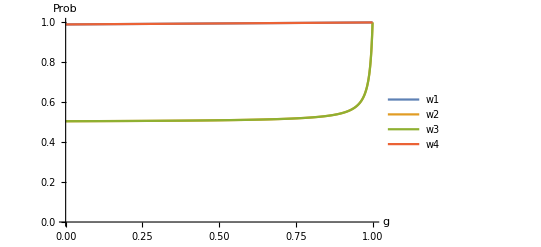

```mathematica
Plot[Evaluate[{w1,w2,w3,w4}//.{ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g","Prob"},PlotRange->{0,1},PlotLegends->{"w1","w2","w3","w4"}]
```